```mathematica
ClearAll["Global`*"];
SetDirectory[NotebookDirectory[]];
```

# NV-Centre ESR Simulation

Construct a Hamiltonian of the form:

Ĥ =

Features to add:
- Enable truncated spin matrices
- Visualisation for the angular momentum conserving transitions
- Visualisation of the energies of the NV-center subsystem states
- Add Plot to RunSimulation function arguments
- Make RunSimulation add to a given list, instead of returning a list
- Make the freqStep dependent on the gradient of the curve. Instead of freqStep you could specify, number of datapoints per unit length on graph curve

## Initialisation

## NV-Centre constants

```mathematica
γN = 19.331*10^6; (* Gyromagnetic ratio for^14 N [s^-1 T^-1] *)
γe = 1.7609*10^11; (* Gyromagnetic ratio for e- [rad s^-1 T^-1] *)
Ahf = { -2.1*10^6, -2.1*10^6, -2.16*10^6 }; (* Hyperfine interaction (x,y,z) [Hz] *)
Dzfs = 2870*10^6 ; (* Zero-field-splitting for electron triplet [Hz] *)
Pzfs = -4.95*10^6 ; (* Zero-field-splitting for^14 N [Hz] *)
```

## Functions

#### GetSubsystemA[density, subSystemSize]

For a density matrix ρ in the space A_1 ⊗ A_2 ⊗ ... ⊗ A_n, the function will return the reduced density matrix ρ_A_1.

```mathematica
GetSubsystemA[density_,subSystemSize_]:=Map[Tr,Partition[density,{Length[density]/subSystemSize,Length[density]/subSystemSize}],{2}];
```

#### FullHilbertSpaceOperator[operators, hilbertSubspaces]

Returns the matrix representation of an operator (Ô)_1⊗(Ô)_2⊗...⊗(Ô)_n. The variable operators should contain a list of pairs, where the second element is the operator acting on subsystem i, and where the first element is i. hilbertSubspaces is a list of the dimensions of the subspaces. Any unspecified operators for the subspaces will be replaced by an identity matrix of the appropriate size.F

```mathematica
FullHilbertSpaceOperator[elem_ /; IntegerQ[elem[[1]]], hilbertSubspaces_] := FullHilbertSpaceOperator[{elem}, hilbertSubspaces];

FullHilbertSpaceOperator[ops_:{ elem_ /; IntegerQ[elem[[1]]] ..} , hilbertSubspaces_] := Module[
{operator = {1}, next},
Do[

next = Select[ ops, #[[1]] == i &];
next = If[next == {}, IdentityMatrix[hilbertSubspaces[[i]]], next[[1]][[2]]];
operator = KroneckerProduct[operator, next];
,{i, 1, Length[hilbertSubspaces]}];

operator
];
```

#### SpinMatrixX[spin]

```mathematica
SpinMatrixX[spin_] :=Table[
(i,j+1  + i+1,j)1/2 Sqrt[spin(spin+1) - i*j]
,{i, spin, -spin,-1},{j,spin, -spin, -1}]
```

#### SpinMatrixY[spin]

```mathematica
SpinMatrixY[spin_] :=Table[
(i,j+1  - i+1,j)1/(2 I)Sqrt[spin(spin+1) - i*j]
,{i, spin, -spin, -1},{j, spin, -spin, -1}]
```

#### SpinMatrixZ[spin]

```mathematica
SpinMatrixZ[spin_] :=Table[
i,j  j
,{i, spin, -spin, -1},{j, spin, -spin, -1}]
```

#### SpinMatrix[j, spin]

Returns the spin matrix (Ŝ)_j

```mathematica
SpinMatrix[j_/; Mod[j-1, 3] == 0, spin_] := SpinMatrixX[spin];
SpinMatrix[j_/; Mod[j-1, 3] == 1, spin_] := SpinMatrixY[spin];
SpinMatrix[j_/; Mod[j-1, 3] == 2, spin_] := SpinMatrixZ[spin];
```

#### SpinSpinHamiltonian[spins, couplings]

Returns a Hamiltonian of the form ∑_ij k_ij (Ŝ)_i. (Ŝ)_j.

Arguments:

spins - List of spins in the system 
couplings - List of elements of the form {indexOfSpin1 → indexOfSpin2, couplingConstant}.

```mathematica
SpinSpinHamiltonian[spins_, couplings_ : { { _ -> _,  _} ..}] := Module[
{H, spin1, spin2, sx, sy,sz, i, j, coeffs},

H = ConstantArray[0, {Times @@ (2spins + 1),Times @@ (2spins + 1)}];

Do[
i = c[[1]][[1]] ;
j = c[[1]][[2]] ;
coeffs = {};

Which[
NumberQ[c[[2]]],
coeffs = {c[[2]], c[[2]], c[[2]]},
Length[c[[2]]] == 3,
coeffs = c[[2]]
];

H = H + Sum[
coeffs[[k]]*FullHilbertSpaceOperator[ 
i->  SpinMatrix[k, spins[[i]]],
2*spins+1
] .FullHilbertSpaceOperator[ 
j ->  SpinMatrix[k, spins[[j]]],
2*spins+1
]
,{k, 1, 3}];

,{c, couplings}];
H
];
```

#### ZeemanHamiltonian[spins, ωs]

Returns a Zeeman Hamiltonian of the specified spins.

```mathematica
ZeemanHamiltonian[spins_, ωs_] :=Sum[
ωs[[i]]*FullHilbertSpaceOperator[i ->  SpinMatrixZ[spins[[i]]], 2spins+1]
,{i, 1, Length[spins]}]
```

#### NVCenterEnergySpectrum[ℋ, spins]

s

```mathematica
NVCenterEnergySpectrum[ℋ_, spins_] := Module[
{basis, mult = 2spins + 1, eig, energies, states,vecDecomps , vecsIndices, vecs, strs,
coeff, label,Jz, angMoms, table, data },
basis[indices_]:= Apply[KroneckerProduct, Table[
RotateRight[Flatten[IdentityMatrix[{1,mult[[i]]}]], indices[[i]]  - 1]
,{i, 1, Length[spins]}]] // Flatten;

eig = Eigensystem[ℋ];
energies = eig[[1]];
states = eig[[2]];

vecDecomps = {};
Do[
vecsIndices = Tuples[Map[Range, mult]];
vecs = Map[ basis, vecsIndices];
strs = {};
Do[
coeff = Conjugate[vecs[[i]]] . states[[k]];
label = Style["|"<>StringRiffle[Table[ (spins[[j]]-vecsIndices[[i]][[j]] + 1)//Rationalize, {j, 1, Length[spins]}],","]<>"⟩", Bold];

If[ coeff ≠ 0, AppendTo[strs,coeff * label]];
,{i, 1, Length[vecsIndices]}];

AppendTo[vecDecomps, strs];
,{k, 1, Length[states]}];

Jz = FullHilbertSpaceOperator[{1 -> SpinMatrixZ[spins[[1]] ]}  , mult] +
FullHilbertSpaceOperator[{2 -> SpinMatrixZ[spins[[2]] ]}  ,mult];
angMoms = Map[ # . Jz . # &, states];

data = {
energies,
vecDecomps,
angMoms
};

data = Sort[Transpose[data], #1[[1]] > #2[[1]] &] // Transpose; 

table = {
Prepend[Prepend[data[[1]], "---"], Style["E", Bold]],
Prepend[ Prepend[data[[2]], "---"], Style["|ψ_E⟩", Bold]],
Prepend[Prepend[data[[3]], "---"],  Style["⟨J_z⟩", Bold]]
} // Transpose //MatrixForm;
{data, table}
];
```

#### GetSybsystemA[density, subSystemSize]

For a density matrix ρ in the space A_1 ⊗ A_2 ⊗ ... ⊗ A_n, the function will return the reduced density matrix ρ_A_1.

```mathematica
GetSubsystemA[density_, subSystemSize_] := Map[ Tr, Partition[ density, {Length[density]/subSystemSize, Length[density]/subSystemSize}], {2}];
```

#### RunSimulation[freqStart, freqEnd, freqStep, ℋ, spins, spinVec, density0]

sd

```mathematica
RunSimulation[freqStart_, freqEnd_, freqStep_, tStart_, tEnd_, ℋ_, spins_, spinVec_, density0_] := Module[
{calculations,systemSize, density, eqnTotal, eqns, diffeqs, funcs, initialStateEqs, params,
data, tic, count, sol, pulseFreq, pFunc, p, prw, toc, ttot},
calculations = Table[f, {f, freqStart, freqEnd, freqStep}] // Length;

(* Setup Density matrix *)
systemSize = Apply[Times, 2spins+1];
density = Table[ ρ[i, j][t],{i, 1, systemSize}, {j, 1, systemSize}] ;
Do[
density[[j, i]] = Conjugate[density[[i,j]]];
, {i, 1, systemSize}, {j, i+1, systemSize}];

(* Define master equation *)

eqnTotal = ⅈ  D[ density, t] - (ℋ[f, t].density - density.ℋ[f, t]) // Simplify;

eqns = Table[ eqnTotal[[i, j]],  {i, 1, systemSize}, {j, i, systemSize}] // Flatten;
diffeqs = Table[ eqns[[i]] == 0, {i, 1, Length[eqns]}];
funcs =Table[ density[[i, j]],  {i, 1, systemSize}, {j, i, systemSize}] // Flatten;
initialStateEqs =  Table[ ρ[i, j][0] == density0[[i, j]],  {i, 1, systemSize}, {j, i, systemSize}]  // Flatten;
params = { diffeqs, initialStateEqs } // Flatten;

(* Perform simulation *)

data = {}; (* Store spinVec probability data for each frequency *)
tic=AbsoluteTime[];
count = 1;

plot =Dynamic[ListPlot[data], TrackedSymbols:>{data}];
Print[plot];

Do[
sol = NDSolve[ params /. f -> freq, funcs, {t, tStart, tEnd}, 
PrecisionGoal->7,AccuracyGoal->7, MaxSteps->Infinity];

(* Take electron triplet sybsystem of state*)
pFunc = Conjugate[spinVec] . GetSubsystemA[density, systemSize/(spins[[1]]*2 + 1)] . spinVec;
p = 1/(tEnd - tStart)NIntegrate[pFunc /. sol, {t, tStart, tEnd}];

AppendTo[data, {freq, p[[1]]}];
NotebookDelete[prw];
prw = PrintTemporary["Calculation ", count, " out of ", calculations];
count = count + 1;

, {freq, freqStart, freqEnd, freqStep}];

toc=AbsoluteTime[];
ttot = N[(toc-tic)/60];
Print["Total time taken (min) = ",ttot];

{data, ttot}

];
```

# No spin-bath

### Initialisation

#### Simulation parameters

```mathematica
pulseAmplitude = 7*10^6; (* [Hz] *)
pulsePhase = 0;

pulseFreqStart = 2.575*10^9; (* [Hz] *)
pulseFreqEnd = 3.175*10^9; (* [Hz] *) 
pulseFreqStep = 0.1*10^6; (* [Hz] *) 
calculations = Table[f, {f, pulseFreqStart, pulseFreqEnd, pulseFreqStep}] // Length;

tStart = 0; (* Start-time of NDSolve [s] *)
tEnd = 2*10^-6; (* End-time of NDSolve [s] *)

B0 =0*513 *10^-4 (* DC Applied field [T] *);
ωs= (-γe B0)/(2π); (* [Hz] *)
ωI=(γN B0)/(2π); (* [Hz] *)

Print["Number of calculations: ", calculations];
```

Number of calculations: 6001

#### Setup Hamiltonian

```mathematica
spins = {1, 1};

ℋHF = 2π * SpinSpinHamiltonian[
spins,
{
{1 -> 2, Ahf}
}
];

ℋspinSpin = 2π *  SpinSpinHamiltonian[
spins,
{{1 -> 1, {0, 0,Dzfs}},
{2 -> 2, {0, 0, Pzfs}}}
] ;

ℋzee = 2π *  ZeemanHamiltonian[spins, {ωs, ωI, 0}];

ℋNV = ℋHF + ℋspinSpin + ℋzee;

ℋCop = 2π *  pulseAmplitude* FullHilbertSpaceOperator[ { 1-> SpinMatrixX[1], 2-> SpinMatrixX[1] }, {3, 3} ] ;
ℋC[f_, t_] :=ℋCop * Sin[2π f t + pulsePhase];

ℋ[f_,t_] := ℋNV  + ℋC[f,t];
```

#### Initial state

```mathematica
eig = Eigensystem[ℋNV];
groundState = {eig[[2]][[Position[eig[[1]], Min[eig[[1]]]][[1]][[1]]]]} // Transpose;
density0 = groundState . ConjugateTranspose[groundState] ;
```

```mathematica
Min[eig[[1]]]*2 Pi
```

-1.95479×10^8

#### Meta

```mathematica
fileNamePrefix = "results/nv_center_simulation_NO_SPIN_BATH"  <> StringReplace[ DateString["ISODateTime"], ":" -> "."];
comments = StringRiffle[{
"Pulse that acts on both nuclear spin and electron spin",
StringForm["B0=``T",B0],
StringForm["Frequency Resolution=``Hz", pulseFreqStep],
StringForm["Pulse amplitude=``Hz", pulseAmplitude]
}, ". "];
```

### Run simulation

```mathematica
spinVec = {0, 1, 0};
res = RunSimulation[pulseFreqStart,pulseFreqEnd, pulseFreqStep, tStart, tEnd, ℋ,spins,spinVec,density0];
data = res[[1]];
totalSimulationTime = res[[2]];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.56219×10^-7}. NIntegrate obtained 1.9999×10^-6-2.82114×10^-25 ⅈ and 3.78361×10^-12 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.42938×10^-7}. NIntegrate obtained 1.99994×10^-6+9.83927×10^-26 ⅈ and 3.71147×10^-12 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

Total time taken (min) = 3012.24

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.56219×10^-7}. NIntegrate obtained 1.99994×10^-6-6.30586×10^-27 ⅈ and 3.78961×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

### Results

#### Energy spectrum of the unperturbed Hamiltonian

```mathematica
hamiltonianSpectrum = NVCenterEnergySpectrum[ℋNV, spins][[2]]
```

(E | |ψ_E⟩ | ⟨J_z⟩
--- | --- | ---
1.80328×10^10 | {1. |1,0⟩,-0.000730447 |0,1⟩} | 1.
1.80328×10^10 | {-0.000730447 |0,-1⟩,1. |-1,0⟩} | -1.
1.80152×10^10 | {0.707106 |1,-1⟩,-0.0010358 |0,0⟩,0.707106 |-1,1⟩} | 0.
1.80152×10^10 | {-0.707107 |1,-1⟩,5.84881×10^-19 |0,0⟩,0.707107 |-1,1⟩} | 0.
1.79881×10^10 | {1. |-1,-1⟩} | -2.
1.79881×10^10 | {1. |1,1⟩} | 2.
-19328.1 | {0.000732418 |1,-1⟩,0.999999 |0,0⟩,0.000732418 |-1,1⟩} | 0.
-3.11114×10^7 | {0.000730447 |1,0⟩,1. |0,1⟩} | 1.
-3.11114×10^7 | {1. |0,-1⟩,0.000730447 |-1,0⟩} | -1.)

#### Simulation results

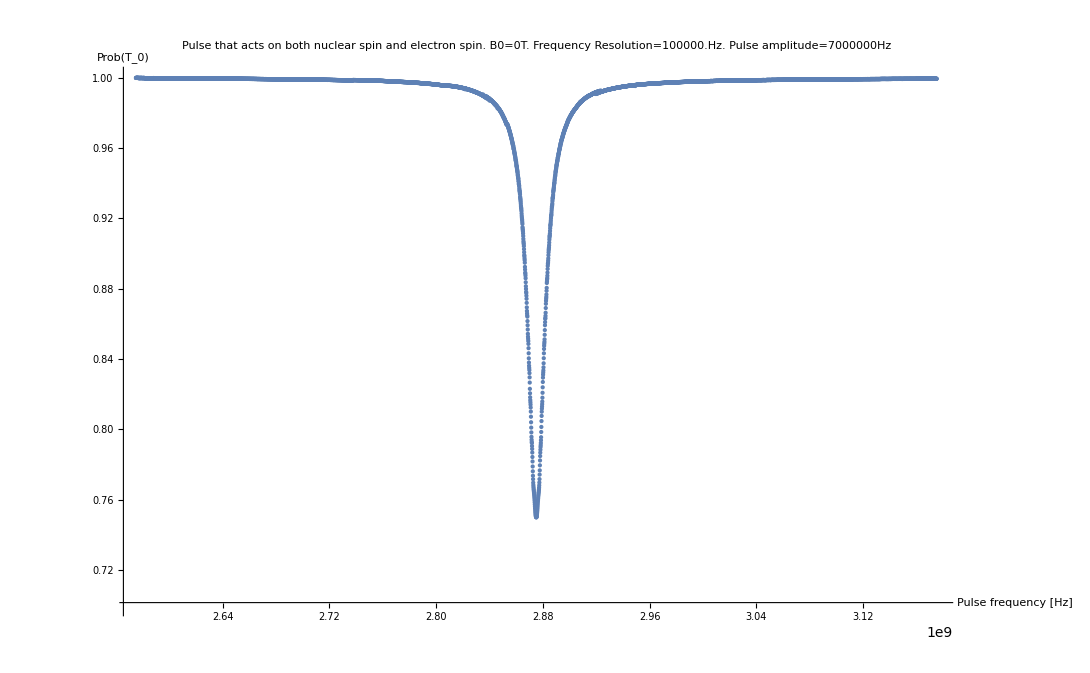

```mathematica
plot = ListPlot[data, PlotLabel->Style[comments, 12], AxesLabel -> { "Pulse frequency [Hz]", "Prob(T_0)"}, PlotRange->{0.7, 1}, ImageSize -> Large ]
```

#### Save simulation data

```mathematica
Export[fileNamePrefix<> "_data.csv", data];
Export[fileNamePrefix<> "_spectrum.csv", hamiltonianSpectrum];
Export[fileNamePrefix<> "_plot.pdf", plot];
Save[ fileNamePrefix <> "_params.dat", {  comments, totalSimulationTime, pulseAmplitude,pulsePhase,pulseFreqStart,pulseFreqEnd,calculations,pulseFreqStep,γN,γe,B0,ωs,ωI,Ahf,Dzfs,Pzfs}];
```

# With spin-bath

### Initialisation

#### Simulation parameters

```mathematica
pulseAmplitude = 7*10^6; (* [Hz] *)
pulsePhase = 0;

pulseFreqStart = 2.86*10^9; (* [Hz] *)
pulseFreqEnd = 2.881*10^9; (* [Hz] *) 
pulseFreqStep = 1*10^6; (* [Hz] *) 
calculations = Table[f, {f, pulseFreqStart, pulseFreqEnd, pulseFreqStep}] // Length;

tStart = 0; (* Start-time of NDSolve [s] *)
tEnd = 2*10^-6; (* End-time of NDSolve [s] *)

B0 =0*513 *10^-4 (* DC Applied field [T] *);
ωs= (-γe B0)/(2π); (* [Hz] *)
ωI=(γN B0)/(2π); (* [Hz] *)
```

#### Setup Hamiltonian

```mathematica
spins = {1, 1, 1/2};

ℋHF = SpinSpinHamiltonian[
spins,
{
{1 -> 2, Ahf},
{1 -> 3, Ahf[[3]]/2}
}
];

ℋspinSpin = SpinSpinHamiltonian[
spins,
{{1 -> 1, {0, 0,Dzfs}},
{2 -> 2, {0, 0, Pzfs}}}
];

ℋzee = ZeemanHamiltonian[spins, {ωs, ωI, 0}];

ℋNV = ℋHF + ℋspinSpin + ℋzee;

ℋC[f_, δ_, t_] = pulseAmplitude* FullHilbertSpaceOperator[ { 1-> SpinMatrixX[1], 2-> SpinMatrixX[1] }, 2spins + 1 ] * Sin[2π f t + δ];

ℋ[f_, δ_, t_] := ℋNV  + ℋC[f, δ, t];
```

#### Initial state

```mathematica
eig = Eigensystem[ℋNV];
groundState = {eig[[2]][[Position[eig[[1]], Min[eig[[1]]]][[1]][[1]]]]} // Transpose;
density0 = groundState . ConjugateTranspose[groundState] ;
```

#### Meta

```mathematica
fileNamePrefix = "results/nv_center_simulation"  <> StringReplace[ DateString["ISODateTime"], ":" -> "."];
comments = StringRiffle[{
"Pulse that acts on both nuclear spin and electron spin",
StringForm["B0=``T",B0],
StringForm["Frequency Resolution=``Hz", pulseFreqStep],
StringForm["Pulse amplitude=``Hz", pulseAmplitude]
}, ". "];
```

### Results

#### Energy spectrum of the unperturbed Hamiltonian

```mathematica
NVCenterEnergySpectrum[ℋNV, spins][[2]]
```

(E | |ψ_E⟩ | ⟨J_z⟩
--- | --- | ---
2.87054×10^9 | {-0.000400223 |1,-1,-0.5⟩,0.000266437 |0,0,-0.5⟩,0.000730416 |0,-1,0.5⟩,-5.55112×10^-17 |0,-1,-0.5⟩,-5.20959×10^-17 |-1,1,0.5⟩,-0.000144513 |-1,1,-0.5⟩,-1. |-1,0,0.5⟩} | -1.
2.87054×10^9 | {-1.80483×10^-17 |1,1,-0.5⟩,-4.21057×10^-17 |1,0,0.5⟩,-1. |1,0,-0.5⟩,-0.000144513 |1,-1,0.5⟩,0.000730416 |0,1,-0.5⟩,0.000266437 |0,0,0.5⟩,5.72663×10^-21 |0,-1,0.5⟩,1.61708×10^-20 |0,-1,-0.5⟩,-0.000400223 |-1,1,0.5⟩} | 1.
2.86946×10^9 | {-0.000730609 |0,-1,-0.5⟩,1. |-1,0,-0.5⟩,0.0000925051 |-1,-1,0.5⟩} | -1.
2.86946×10^9 | {-0.0000925051 |1,1,-0.5⟩,-1. |1,0,0.5⟩,-4.91365×10^-17 |1,0,-0.5⟩,-4.61379×10^-17 |1,-1,0.5⟩,0.000730609 |0,1,0.5⟩,-1.2746×10^-19 |0,1,-0.5⟩,2.24098×10^-33 |0,-1,0.5⟩,-3.00459×10^-33 |0,-1,-0.5⟩,6.39151×10^-17 |-1,1,0.5⟩} | 1.
2.86775×10^9 | {-0.999999 |1,-1,-0.5⟩,0.000733216 |0,0,-0.5⟩,0.000265545 |0,-1,0.5⟩,-1.11022×10^-16 |0,-1,-0.5⟩,1.00831×10^-17 |-1,1,0.5⟩,-0.0014234 |-1,1,-0.5⟩,0.000400818 |-1,0,0.5⟩} | -2.31169×10^-7
2.86775×10^9 | {-4.20431×10^-17 |1,1,-0.5⟩,1.39073×10^-16 |1,0,0.5⟩,-0.000400818 |1,0,-0.5⟩,0.0014234 |1,-1,0.5⟩,2.22045×10^-16 |0,1,0.5⟩,-0.000265545 |0,1,-0.5⟩,-0.000733216 |0,0,0.5⟩,-1.73772×10^-17 |0,-1,0.5⟩,5.29928×10^-17 |0,-1,-0.5⟩,0.999999 |-1,1,0.5⟩} | 2.31169×10^-7
2.86667×10^9 | {4.17693×10^-17 |1,1,-0.5⟩,-7.95066×10^-17 |1,0,0.5⟩,-0.000144138 |1,0,-0.5⟩,0.999999 |1,-1,0.5⟩,2.1684×10^-19 |1,-1,-0.5⟩,-1.11022×10^-16 |0,1,0.5⟩,4.84102×10^-7 |0,1,-0.5⟩,-0.000731474 |0,0,0.5⟩,7.07801×10^-20 |0,-1,0.5⟩,1.5659×10^-19 |0,-1,-0.5⟩,-0.00142399 |-1,1,0.5⟩} | 2.0776×10^-8
2.86667×10^9 | {-0.00142399 |1,-1,-0.5⟩,-0.000731474 |0,0,-0.5⟩,4.84102×10^-7 |0,-1,0.5⟩,-2.1684×10^-19 |0,-1,-0.5⟩,0.999999 |-1,1,-0.5⟩,-0.000144138 |-1,0,0.5⟩} | -2.0776×10^-8
2.86343×10^9 | {-0.000266171 |0,-1,-0.5⟩,-0.0000926996 |-1,0,-0.5⟩,1. |-1,-1,0.5⟩} | -2.
2.86343×10^9 | {-1. |1,1,-0.5⟩,0.0000926996 |1,0,0.5⟩,-3.78253×10^-18 |1,0,-0.5⟩,-3.53255×10^-18 |1,-1,0.5⟩,-7.70372×10^-34 |1,-1,-0.5⟩,0.000266171 |0,1,0.5⟩,-6.43669×10^-20 |0,1,-0.5⟩,-2.77942×10^-35 |0,-1,0.5⟩,5.08956×10^-18 |-1,1,0.5⟩,-7.70372×10^-34 |-1,0,0.5⟩} | 2.
2.86235×10^9 | {1. |1,1,0.5⟩} | 2.
2.86235×10^9 | {1. |-1,-1,-0.5⟩} | -2.
-4.95174×10^6 | {1. |0,-1,-0.5⟩,0.000730584 |-1,0,-0.5⟩,0.000266239 |-1,-1,0.5⟩} | -1.
-4.95174×10^6 | {0.000266239 |1,1,-0.5⟩,0.000730584 |1,0,0.5⟩,2.98939×10^-10 |1,0,-0.5⟩,6.76142×10^-14 |1,-1,0.5⟩,1. |0,1,0.5⟩,4.09297×10^-7 |0,1,-0.5⟩,9.2305×10^-11 |0,0,0.5⟩,-8.80776×10^-27 |0,-1,0.5⟩,3.48327×10^-27 |0,-1,-0.5⟩,1.08875×10^-10 |-1,1,0.5⟩} | 1.
-4.95174×10^6 | {-1.08971×10^-10 |1,1,-0.5⟩,-2.99026×10^-10 |1,0,0.5⟩,0.00073037 |1,0,-0.5⟩,1.64922×10^-7 |1,-1,0.5⟩,-4.09297×10^-7 |0,1,0.5⟩,1. |0,1,-0.5⟩,0.000225521 |0,0,0.5⟩,-1.21361×10^-20 |0,-1,0.5⟩,-4.50092×10^-22 |0,-1,-0.5⟩,0.000266003 |-1,1,0.5⟩} | 1.
-4.95174×10^6 | {-0.000266003 |1,-1,-0.5⟩,-0.000225521 |0,0,-0.5⟩,-1. |0,-1,0.5⟩,2.35272×10^-17 |0,-1,-0.5⟩,-5.2882×10^-17 |-1,1,0.5⟩,-1.64922×10^-7 |-1,1,-0.5⟩,-0.00073037 |-1,0,0.5⟩} | -1.
-3279.07 | {3.14675×10^-21 |1,1,-0.5⟩,8.61361×10^-21 |1,0,0.5⟩,0.000265873 |1,0,-0.5⟩,0.000732556 |1,-1,0.5⟩,1.17636×10^-17 |0,1,0.5⟩,-0.00022591 |0,1,-0.5⟩,0.999999 |0,0,0.5⟩,1.50575×10^-20 |0,-1,0.5⟩,9.07833×10^-22 |0,-1,-0.5⟩,0.00073222 |-1,1,0.5⟩} | 1.21724×10^-7
-3279.07 | {0.00073222 |1,-1,-0.5⟩,0.999999 |0,0,-0.5⟩,-0.00022591 |0,-1,0.5⟩,-1.0842×10^-19 |0,-1,-0.5⟩,0.000732556 |-1,1,-0.5⟩,0.000265873 |-1,0,0.5⟩} | -1.21724×10^-7)

#### Simulation results